## Potential of a 2 D thin slab extended from -∞ to +∞ along y and from -a/2 to a/2 along z

#### Marco Gibertini and Giovanni Pizzi, May 2013

We calculate the electric field on the x axis, that for symmetry reasons will be oriented along x. We sum together the 4 contributions from the four points (-x,-z), (-x,+z), (+x,-z) and (+x,+z) considering a factor of 4, only the x component of the electric field, and integrating only on 1/4 of the slab.

Note : we consider a slab with linear charge density λ (charge per unit length along y), having thus a surface density σ=λ/a

Note : we don’t calculate directly the potential energy because the integral would diverge if we choose the zero of the potential at infinity. We instead first obtain the electric field and then integrate to obtain the potential energy, setting the zero at the slab position.

Electric field for x>0. Each contribution (dydz) has charge q = σ * (dydz) and contributes with a field q/r^2; I integrate the x component only

```mathematica
Epos = Integrate[(4 x * λ/a)/((x^2+y^2+z^2)^(3/2)),{y,0,∞},{z,0,a/2},Assumptions-> {λ>0,x>0,a>0}]
```

(4 λ ArcCos[(2 x)/(√(a^2+4 x^2))])/a

```mathematica
Eneg = Integrate[(4 x * λ/a)/((x^2+y^2+z^2)^(3/2)),{y,0,∞},{z,0,a/2},Assumptions-> {λ>0,x<0,a>0}]
```

(4 λ (-π+ArcCos[(2 x)/(√(a^2+4 x^2))]))/a

```mathematica
Efield[x_,λ_,a_]:=(4 λ (-π UnitStep[-x]+ArcCos[(2 x)/(√(a^2+4 x^2))]))/a
```

```mathematica
Manipulate[Plot[Efield[x,1,a],{x,-4,4},PlotRange-> {-2π,2π}],{a,0.001,20}]
```

I calculate the potential energy at coordinate x0 by integration of the eletric field, setting the zero of the potential at the slab position. I do it independently for x>0 and x<0.

```mathematica
Vpos = (4λ)/a Integrate[ArcCos[(2 x)/(√(a^2+4 x^2))],{x,0,x0},Assumptions->{x0>0,a>0}]
```

(4 λ (x0 ArcCos[(2 x0)/(√(a^2+4 x0^2))]+1/4 a Log[1+(4 x0^2)/a^2]))/a

```mathematica
Vneg= (4λ)/a Integrate[-π+ArcCos[(2 x)/(√(a^2+4 x^2))],{x,0,x0},Assumptions->{x0<0,a>0}]
```

(4 λ (-π x0+x0 ArcCos[(2 x0)/(√(a^2+4 x0^2))]+1/4 a Log[1+(4 x0^2)/a^2]))/a

I write down the obtained potential on the whole x axis

```mathematica
V[x_,λ_,a_]:=4λ/a(-π x UnitStep[-x]+x ArcCos[(2 x)/(√(a^2+4 x^2))]+1/4 a Log[1+(4 x^2)/a^2])
```

```mathematica
Manipulate[Plot[V[x,1,a],{x,-4,4},PlotRange-> {-10,10}],{a,0.01,20}]
```

## Potential of a 1D wire

We realized that the limit a→ 0 is well-defined and that in this limit the calculation of the electric field due to an infinite set of periodic replicas of the wire is very simple.

```mathematica
Limit[Epos,a->0,Assumptions-> {x>0}]
```

(2 λ)/x

```mathematica
Limit[Eneg,a->0,Assumptions-> {x<0}]
```

(2 λ)/x

Let us now consider an infinite periodic system. The distance between consecutive periodic replicas of the wire is δ. If we consider x to be in the range [0,δ] then the electric field is given by

```mathematica
E(x) =∑_(n=-∞)^(+∞) (2λ)/(x- n δ)= (2λ)/(ξ δ) + (4λ ξ)/δ ∑_(n=1)^(+∞) 1/(ξ^2-n^2)
```

where ξ = x/δ.

The sum can be easily computed

```mathematica
Sum[1/(ξ^2-n^2),{n,1,∞},Assumptions->{0<ξ<1}]
```

(-1+π ξ Cot[π ξ])/(2 ξ^2)

So that the electric field is

```mathematica
Eper[ξ_,λ_,δ_] := (2 π λ Cot[π ξ])/δ;
```

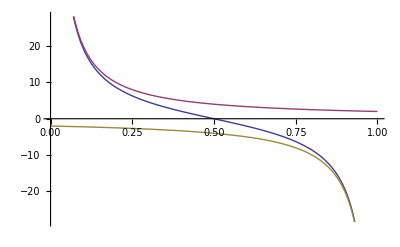

```mathematica
Plot[Evaluate[{Eper[ξ,λ,δ],(2λ)/(ξ δ),(2λ)/(δ(ξ-1))}/.{λ-> 1,δ-> 1}],{ξ,0,1}]
```